```mathematica
config={A->1,Ts->1/100,f0->100/10,σ->1/5}
```

{A→1,Ts→1/100,f0→10,σ→1/5}

```mathematica
x[t_]=A*Exp[-t^2/(2σ^2)]*Cos[2Pi*f0*t]/.config
```

ⅇ^(-(25 t^2)/2) Cos[20 π t]

```mathematica
xd0[n_]=x[n*Ts]/.config
```

ⅇ^(-n^2/800) Cos[(n π)/5]

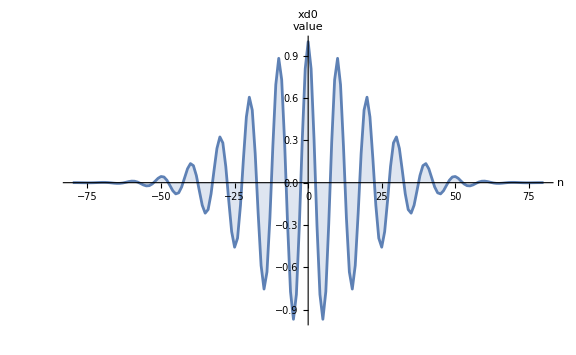

```mathematica
Block[{N0=1/(f0*Ts)/.config},
DiscretePlot[xd0[n],{n,-8N0,8N0},PlotRange->Full,PlotLabel->"xd0",AxesLabel->{"n","value"},ImageSize->Large]
]
```

```mathematica
X0[f_]=Block[{Ts=Ts/.config,σ=σ/.config},
Sum[xd0[n]*Exp[-I*2Pi*f*n*Ts],{n,-5σ/Ts,5σ/Ts}]
];
tilde X0[f_]=X0[f/Ts]/.config;
```

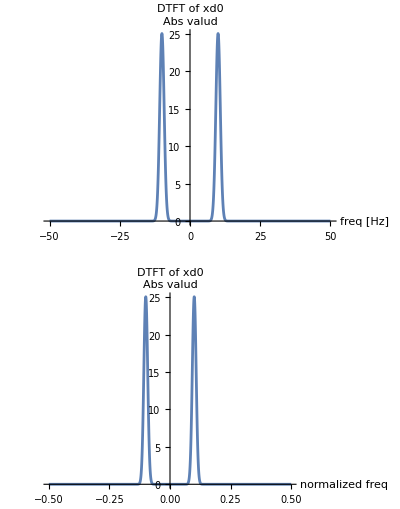

```mathematica
Block[{Ts=Ts/.config,p1,p2},
p1=Plot[Abs[X0[f]],{f,-1/(2Ts),1/(2Ts)},PlotRange->Full,PlotLabel->"DTFT of xd0",AxesLabel->{"freq [Hz]","Abs valud"},ImageSize->Large];
p2=Plot[Abs[tilde X0[f]],{f,-1/2,1/2},PlotRange->Full,PlotLabel->"DTFT of xd0",AxesLabel->{"normalized freq","Abs valud"},ImageSize->Large];
GraphicsGrid[{{p1},{p2}}]
]
```

```mathematica
xd1[n_]:=If[EvenQ[n],xd0[n/2],0]
```

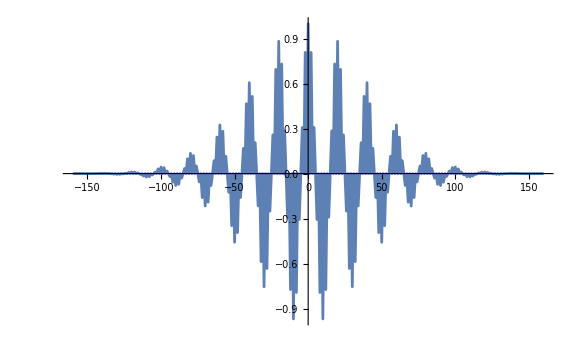

```mathematica
Block[{N0=1/(f0*Ts/2)/.config},
DiscretePlot[xd1[n],{n,-8N0,8N0},PlotRange->Full,ImageSize->Large]
]
```

```mathematica
X1[f_]=Block[{Ts=Ts/.config,σ=σ/.config},
Sum[xd1[n]*Exp[-I*2Pi*f*n*(Ts/2)],{n,-2*5σ/Ts,2*5σ/Ts}]
];
tilde X1[f_]=X1[f/(Ts/2)]/.config;
```

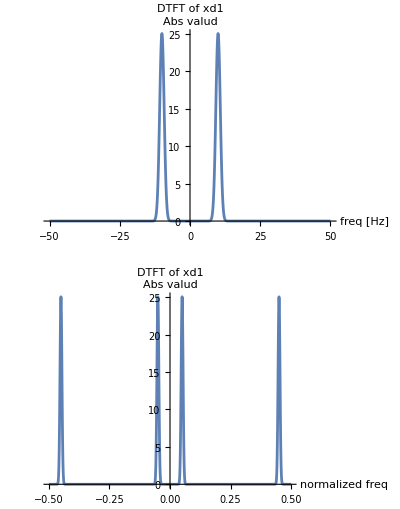

```mathematica
Block[{Ts=Ts/.config,p1,p2},
p1=Plot[Abs[X1[f]],{f,-1/(2Ts),1/(2Ts)},PlotRange->Full,PlotLabel->"DTFT of xd1",AxesLabel->{"freq [Hz]","Abs valud"},ImageSize->Large];
p2=Plot[Abs[tilde X1[f]],{f,-1/2,1/2},PlotRange->Full,PlotLabel->"DTFT of xd1",AxesLabel->{"normalized freq","Abs valud"},ImageSize->Large];
GraphicsGrid[{{p1},{p2}}]
]
```